# Chen et al, FEBS 2007

Chun Chen, Jun Cui, Wei Zhang, Pingping Shen, “Robustness analysis identifies the plausible model of the Bcl-2 apoptotic switch,” FEBS Letters 581 (2007) 5143-5150.

In this paper the authors describe two models, one to represent the direct and the other the indirect pathways to apoptosis, and characterize their relative plausibility as a mechanism for the apoptotic switch based on how robustly they produce a bistable, ultrasensitive switch across a wide range of parameters.

## General Comments

There are a number of features of these models that are (at least in hindsight) questionable.

First, the very set-up of the paper is dubious because the two models ignore things that (I at least) would consider to be well established. For example, the direct model doesn’t include Bcl-2 binding to inhibit Bax (not even the inactive form), whereas the indirect model doesn’t include any activating influence of BH3s on Bax (Bax is instead presumed to simple oligomerize into the mitochondrial activating complex on its own). This is of course the purpose of the paper, to compare these two proposed mechanisms, but each one is such a caricature of the available evidence that it’s not clear what can really be learned from them.

Second, the notion that robustly producing bistability should be the standard for determining mechanistic plausibility is highly problematic.

Third, it appears that the basal steady state level of activated Bax is high in both cases! They even note this on page 5145: “However, high Hill coefficients here do no sufficiently imply ultrasensitive responses since both models have significant basal activations which could make the sensitivity of the responses overestimated.” Given that there is a high basal response, you would imagine that they would take this fact to indicate that the model doesn’t make any sense!!! But instead, they go about measuring the ultrasensitivity of the response as the increase over the basal activity, even though the basal activity represents 85+% of Bax incorporated into pores!!! 

They themselves appear to acknowledge this with the statement “Our results indicate that none of the two models is ultrasensitive, or to say ‘more sensitive than the Michaelis-Menten equation.’”

## Definition of the Equations and Parameters

```mathematica
Remove["Global`*"]

(* Units in nanomolar, nM^-1, and nM^-1 s^-1; see Table 1 *)
params = {
Ena0 -> 2,
Act0  -> 1,
BH30 -> 3,
InBax0 -> 60,
Bcl20 -> 30,
kBH3Bcl2 -> 10^-4,
krBH3Bcl2 -> 10^-3,
kInBax -> 10^-3,
kBax -> 10^-3,
kBaxBcl2 -> 10^-4,
krBaxBcl2 -> 10^-3,
ko -> 10^-3,
kro -> 10^-3,
n -> 4
};

(* INDIRECT *)
IMterms = {
J1i =  kBH3Bcl2 * BH3[t] * Bcl2[t] - krBH3Bcl2 * BH3Bcl2[t],
J2i =  kBaxBcl2 * Bax[t] * Bcl2[t] - krBaxBcl2 * BaxBcl2[t],
J3i =  ko * Bax[t]^n - kro * MAC[t]
};
IMeqns = {
BH3'[t] ==  -J1i,
Bcl2'[t] ==  -J1i - J2i,
BH3Bcl2'[t] ==  J1i,
BaxBcl2'[t] ==  J2i,
Bax'[t] ==  -J2i - (4*J3i),
MAC'[t] ==  J3i
};
IMinitConds = {
BH3[0] == BH30 + BH30 * F,
Bcl2[0] == Bcl20,
BH3Bcl2[0] ==0,
BaxBcl2[0] == 0,
Bax[0] == InBax0,
MAC[0] == 0
};
IMsolveList = {BH3, Bcl2, BH3Bcl2, BaxBcl2, Bax, MAC};

(* DIRECT *)
DMterms = {
(*J1d =  kBH3Bcl2 * Ena[t] * Bcl2[t] - krBH3Bcl2*EnaBcl2[t], *)
J1d = 0,
J2d =  kBH3Bcl2 * Act[t] * Bcl2[t] - krBH3Bcl2*ActBcl2[t],
(*J2d = 0,*)
J3d =  kInBax * Act[t] * InBax[t] - kBax * Bax[t], (* No ES complex for Act+Bax! *)
J4d =  ko * Bax[t]^n- kro * MAC[t]
} ;
DMeqns = {
Ena'[t]== -J1d,
Bcl2'[t] == -J1d - J2d,
EnaBcl2'[t] == J1d,
Act'[t] == -J2d,
ActBcl2'[t] == J2d,
InBax'[t] == -J3d,
Bax'[t] == J3d - (n*J4d),
MAC'[t] == J4d
};
DMinitConds = {
Ena[0] ==  Ena0+ Ena0 * F,
(*Act[0] == Act0+ Act0 * F,*)
Act[0] == Act0 + Act0 * F,
InBax[0] == InBax0,
Bcl2[0] == Bcl20,
EnaBcl2[0] == 0,
ActBcl2[0] == 0,
Bax[0] == 0,
MAC[0] == 0
};
DMsolveList = {Ena, Bcl2, EnaBcl2, Act, ActBcl2, InBax, Bax, MAC};

(* Set the initial conditions *)
DModes = Join[DMeqns, DMinitConds];
IModes = Join[IMeqns, IMinitConds];

(* Run simulations to determine dose response *)
```

## Important Functions

```mathematica
calcSSval[odes_, solveList_, Fval_, tmax_] :=(
 nsoln = NDSolve[odes /. F -> Fval , solveList, {t, 0, tmax}];

(* Get the normalized values at steady state *)
macFun =(MAC /. nsoln)[[1]];
ssMAC = macFun[tmax];
ssMACNorm = (ssMAC * 4) / (InBax0 /. params)
)

activatedFrac[f_, x_, fBasal_, fMax_] := (
(f[x] - fBasal) / (fMax - fBasal)
);
(*activatedFrac[ssVal_, basal_, max_] := (
(ssVal - basal) / (max - basal)
);*)

respCoeff[f_, x0_, dx_] := (
f0 = f[x0];
df = f[x0 + dx] - f0;
(df / f0) / (dx / x0) 
);

DMfunc[F_, modParams_ : {}, tmax_: 10^6] := calcSSval[DModes /. modParams /. params, DMsolveList, F, tmax];
IMfunc[F_, modParams_ : {}, tmax_ : 10^6] := calcSSval[IModes /. modParams /. params,IMsolveList, F, tmax];

hillEqn[x_] := x / (1 + x);

plotMAC[odes_, solveList_, Fval_] := 1

normObs[func_, t_, tot_] := func[t] / tot

(* Plot of key observables of the direct model *)
timecoursePlot[nsoln_, tmax_] := (
macPlot = Plot[normObs[(MAC /. nsoln)[[1]], t, (InBax0 / 4) /. params], {t, 0, tmax}, PlotStyle-> {Thick, Red}, PlotRange-> {0, 1}];
inBaxPlot = Plot[normObs[(InBax /. nsoln)[[1]], t, InBax0 /. params], {t, 0, tmax}, PlotStyle-> {Thick, Blue}, PlotRange-> {0, 1}];
actPlot = Plot[normObs[(Act /. nsoln)[[1]], t, Act0 /. params], {t, 0, tmax}, PlotStyle-> {Thick, Green}, PlotRange-> {0, 1}];
enaPlot = Plot[normObs[(Ena /. nsoln)[[1]], t, Ena0 /. params], {t, 0, tmax}, PlotStyle-> {Thick, Orange}, PlotRange-> {0, 1}];

Show[macPlot, inBaxPlot, actPlot, enaPlot]
)
```

## Baseline Behavior of the Model and Ultrasensitivity Analysis (Figure 2 in the Paper)

### Figure 2a : Dose-response

Compare to Fig 2a in the paper. Note the very high basal response level with the default parameters (85% of Bax is in pores with F = 0!)

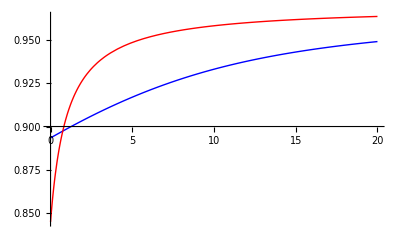

```mathematica
tmax = 100000;
DMfig2A = Plot[DMfunc[i, {}, tmax], {i, 0, 20}, PlotRange -> All, PlotStyle -> {Thick, Red}];
IMfig2A = Plot[IMfunc[i, {}, tmax], {i, 0, 20}, PlotRange -> All, PlotStyle -> {Thick, Blue}];
Show[IMfig2A, DMfig2A]
```

### Figure 2b: Dose-responsive increase over basal activity

Note that what they’re doing here is normalizing the minimum response to the basal level, and the maximum response to the level at F = 10 or F = 20, and then looking at the curvature of the dose-response.

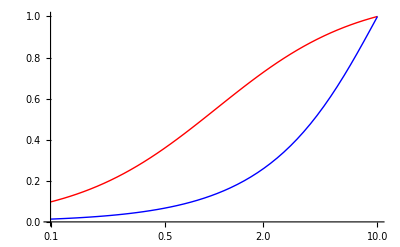

```mathematica
minF = 0.1;
maxF = 10;
tmax = 100000;
DMbasal =calcSSval[DModes /. params, DMsolveList, 0, tmax];
DMmax= calcSSval[DModes /. params, DMsolveList, maxF, tmax];
IMbasal =calcSSval[IModes /. params, IMsolveList, 0, tmax];
IMmax= calcSSval[IModes /. params, IMsolveList, maxF, tmax];

(* Calculates the activated fraction f, per the formula in the supplement *)
DMfig2b = LogLinearPlot[activatedFrac[DMfunc,i,DMbasal, DMmax], {i, minF, maxF}, PlotStyle -> {Thick, Red}, PlotRange-> {0,1}];
IMfig2b = LogLinearPlot[activatedFrac[IMfunc, i, IMbasal, IMmax], {i, minF, maxF}, PlotStyle -> {Thick, Blue}, PlotRange-> {0,1}];

Show[DMfig2b, IMfig2b]
```

### Figure 2c. Relative Amplification Plot

This basically just shows that with the given parameters, both the DM and the IM are far less sensitive than the Hill equation (gray line), across a broad range of activation levels.

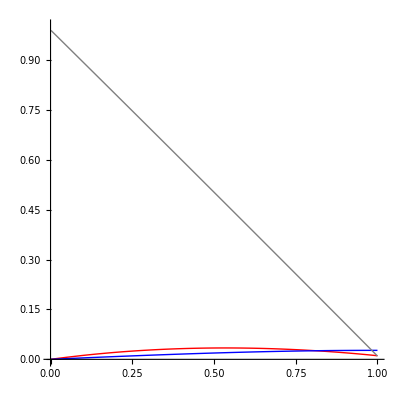

```mathematica
dx = 0.01;
DMrelAmpPlot = ParametricPlot[{activatedFrac[DMfunc,i,DMbasal, DMmax],
			 respCoeff[DMfunc,i, dx]}, {i, 0, 10}, PlotRange -> {0, 1}, PlotStyle -> {Thick, Red}];
IMrelAmpPlot = ParametricPlot[{activatedFrac[IMfunc,i,IMbasal, IMmax],
			 respCoeff[IMfunc,i, dx]}, {i, 0, 10}, PlotRange -> {0, 1}, PlotStyle -> {Thick, Blue}];
hillRelAmpPlot = ParametricPlot[{activatedFrac[hillEqn,i,hillEqn[0], hillEqn[100]],
			 respCoeff[hillEqn, i, dx]}, {i, 0, 100}, PlotRange-> {0, 1}, PlotStyle -> {Thick, Gray}];

Show[DMrelAmpPlot, IMrelAmpPlot, hillRelAmpPlot]
```

## Timecourse Plots

Some observations here. 

First, the authors show that if you increase the BH3/Bcl2 binding affinity in the direct model, you can get a better basal off-state with F = 0 and greater ultrasensitivity (F is set to 2 here only so that the red curve for MAC formation can actually be seen):

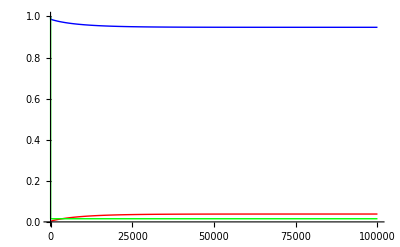

0.0118206

```mathematica
(* kBH3Bcl2 baseline value = 10^-4 *)
tmax = 100000;
nsoln = NDSolve[DModes /. {F -> 3, kBH3Bcl2-> 10^-2} /. params, DMsolveList, {t, 0, tmax}];
timecoursePlot[nsoln, tmax]

DMfunc[0.4, {F -> 2, kBH3Bcl2-> 10^-2} , tmax]
```

However, even in this case of high BH3/Bcl2 binding affinity, if you set both the reverse rate for Bax activation (kBax) to 0 and the reverse rate for oligomerization (kro) to 0, you get 100% activation, even if the basal amount of activator is very low (i.e., if F is 0). Note however, that the timescale of reaching 100% pore formation remains long (on the order of 10^6seconds). See below, red curve (MAC):

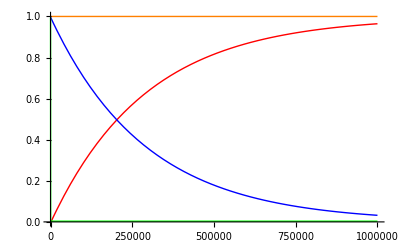

```mathematica
(* kBH3Bcl2 baseline value = 10^-4 *)
tmax = 1000000;
nsoln = NDSolve[DModes /. {F -> 0, kro -> 0, kBax -> 0, kBH3Bcl2-> 10^-2} /. params, DMsolveList, {t, 0, tmax}];
timecoursePlot[nsoln, tmax]
```

In addition, setting only the oligomerization rate kro to 0 (while keeping the activation step as being reversible) dramatically slows the accumulation of MACs, but on very long timescales (e.g. 10^12 seconds) MAC formation eventually reaches 100%:

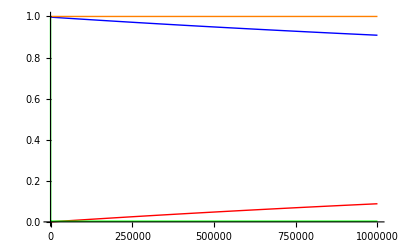

```mathematica
(* kBH3Bcl2 baseline value = 10^-4 *)
tmax = 10^6;
nsoln = NDSolve[DModes /. {F -> 0, kro -> 0, kBH3Bcl2-> 10^-2} /. params, DMsolveList, {t, 0, tmax}];
timecoursePlot[nsoln, tmax]
```

However, setting only the Bax inactivation rate to 0 leads to 100% pore formation much more rapidly. In fact, it is almost indistinguishable from the case where both Bax activation and pore formation are reversible (see above):

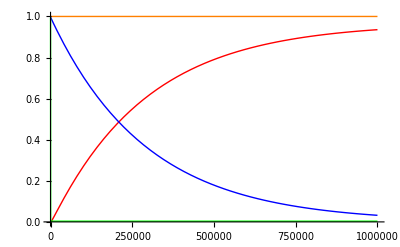

```mathematica
(* kBH3Bcl2 baseline value = 10^-4 *)
tmax = 10^6;
nsoln = NDSolve[DModes /. {F -> 0, kBax -> 0, kBH3Bcl2-> 10^-2} /. params, DMsolveList, {t, 0, tmax}];
timecoursePlot[nsoln, tmax]
```

The greater role of the Bax inactivation rate than the pore disintegration rate is likely due to the fact that MAC formation, being an order-4 reaction, is a process with a longer waiting time than Bax formation. If Bax formation is reversible, this maintains a relatively small pool of active Bax available for the order-4 reaction to occur. If MAC formation is irreversible, MACs will accumulate from this small pool, albeit very slowly. On the other hand, if Bax activation is irreversible, this rapidly leads to an accumulation of all Bax being in the active state, which provides a large pool of Bax available for the "difficult" step of pore formation.

What this indicates is that the fact that the increase in kBH3Bcl2 (Act + Bcl2 binding) can keep the system off is due exclusively to the fact that Bax activation is considered to be reversible in this model.

One interesting question is why the switch from off to on is ultrasensitive in the case where kBH3Bcl2 is high. Is this due to a feature of the binding isotherm between activator and Bcl2 rapidly yielding more free activator in the regime when Activator is in small amounts?[?]

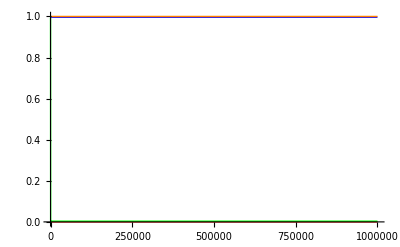

```mathematica
(* kBH3Bcl2 baseline value = 10^-4 *)
tmax = 1000000;
nsoln = NDSolve[DModes /. {F -> 0, kBH3Bcl2-> 10^-2} /. params, DMsolveList, {t, 0, tmax}];
timecoursePlot[nsoln, tmax]
```

## Solution of Steady State Equations

```mathematica
(*
DMsscond = {
Ena'[t] -> 0,
Bcl2'[t] -> 0,
EnaBcl2'[t] ->0,
Act'[t] -> 0,
ActBcl2'[t] -> 0,
InBax'[t] -> 0,
Bax'[t] -> 0,
MAC'[t] -> 0
};

DMconseqns = {
Ena0 ==  Ena[t] + EnaBcl2[t],
Bcl20 == Bcl2[t] + EnaBcl2[t] + ActBcl2[t],
Act0 == Act[t] + ActBcl2[t],
InBax0 == InBax[t] + Bax[t] + n*MAC[t]
};

(*DMparams2 = {
BH30 -> 3,
InBax0 -> 60,
Bcl20 -> 30,
kBH3Bcl2 -> 10^-4,
krBH3Bcl2 -> 10^-3,
kInBax -> 10^-3,
kBax -> 10^-3,
kBaxBcl2 -> 10^-4,
krBaxBcl2 -> 10^-3,
ko -> 10^-3,
kro -> 10^-3,
n -> 4
};*)

DMsseqns = Join[DMeqns, DMconseqns] /. DMsscond  /. params *)
```

```mathematica
(*DMssSoln = Solve[DMsseqns, DMsolveList]*)
```

```mathematica
(*ssMAC = MAC[t] /. sssoln ;
```

```mathematica
(* Correct solution is the third one, verified by checking against the numerical result *)

(*f[x_] := Evaluate[(ssMAC[[3]] /. {Act0 -> x, Ena0 -> 2}) * 4 / (InBax0 /. params)]
Plot[f[g], {g, 0, 2}, PlotRange -> {0, 1}] *)
```